# IIT JAM 2025 Result

## Fitting a Logistics Growth Model to the Data

Naman Taggar

## 1. Introduction

The logistics growth model is defined by the differential equation (d R(m))/(d m)=r R(m) (1-(R(m))/K) with R(m_0)=R_0, where K is the carrying capacity of R(m), and r is the rate at which R(m) changes with respect to m. We are denoting the rank at marks m by R(m). Then, the value of K will be 11000 and r is to be estimated. When R(m)>1, the rate of change will be negative. As R(m)⟶1, (d R(m))/(d m)⟶0. We solve this system along with initial data R(33.33)=1212 (rank-marks pair of one of the students) using DSolve:

```mathematica
sol=DSolve[{R'[m]==r R[m](1-R[m]/11000),R[33.33]==1212},R[m],m]
predict[m_]:=R[m]/.sol//Tr
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{R[m]→(11000. ⅇ^(m r))/(ⅇ^(m r)+8.07591 (ⅇ^(33.33 r))^1.)}}

```mathematica
predict[m]
```

(11000. ⅇ^(m r))/(ⅇ^(m r)+8.07591 (ⅇ^(33.33 r))^1.)

The overall dynamics then look like this, with a dummy value of r:

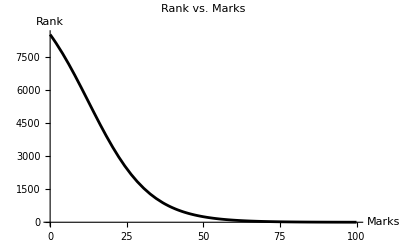

```mathematica
Plot[predict[m]/.r->-.1,{m,0,100},PlotLabel->"Rank vs. Marks",AxesLabel->{"Marks","Rank"},PlotStyle->Black]
```

## 2. Simulation

We store the data {(m_i,R(m_i))}_(i=1)^20 extracted from 20 actual result score-cards found online:

```mathematica
data:={{30.33,1521},{33.33,1212},{79,4},{58,140},{95.33,1},{94,2},{45.44,467},{48,364},{38,841},{66,44},{48.67,336},{54.33,187},{54,194},{62.67,86},{49.33,319},{30.33,1521},{39.67,734},{45.33,467},{49.33,317},{64.67,57}}
```

We fit the model using NonlinearModelFit:

```mathematica
model=NonlinearModelFit[data,predict[m],{r},m]
```

FittedModel[…]

Finally, we see the result:

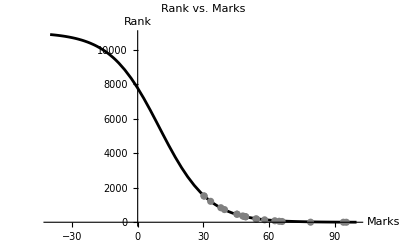

```mathematica
Show[{
Plot[model[m],{m,-40,100},PlotStyle->Black],
ListPlot[data,PlotStyle->Gray]
},PlotLabel->"Rank vs. Marks",AxesLabel->{"Marks","Rank"}]
```

The model can be used to predict rank of varying marks, for example:

```mathematica
TableForm[{#,model@#}&/@Table[i,{i,10,100,10}],TableHeadings->{None,{"Marks","Rank"}}]
```

Marks | Rank
10 | 5465.88
20 | 3174.01
30 | 1570.43
40 | 704.123
50 | 300.474
60 | 125.405
70 | 51.8441
80 | 21.3484
90 | 8.77648
100 | 3.60564

Of course, these are only approximate results, yet fairly accurate.

## References

[1] Barnes, Belinda, and Glenn R. Fulford. Mathematical Modelling with Case Studies: A Differential Equations Approach Using Maple and MATLAB. 2nd ed., CRC Press, 2009.